## Zadanie 1

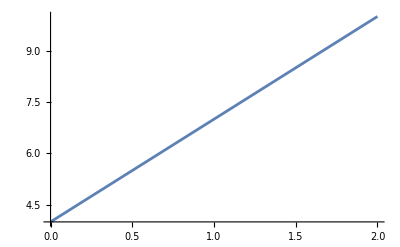

```mathematica
Plot[3x+4,{x,0,2}]
```

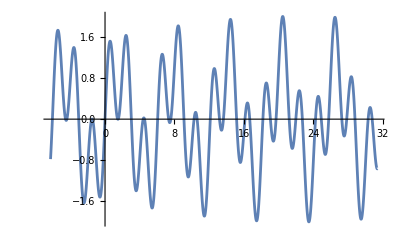

```mathematica
Plot[Sin[x]+Sin[π x],{x,-2π,10π}]
```

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

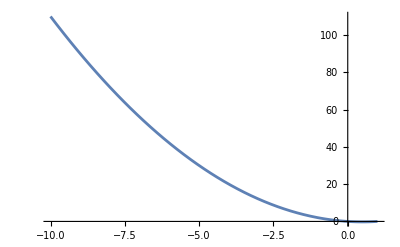

```mathematica
Plot[x^2-x,{x,-10,1}]
```

```mathematica
Plot3D[x^2-y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

## Zadanie 2

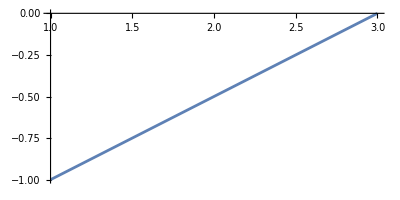

```mathematica
ParametricPlot[{2t+1,t-1},{t,0,1}]
```

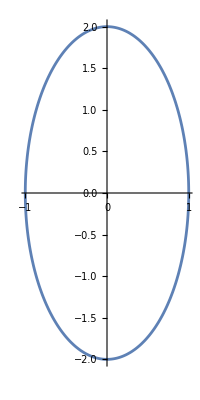

```mathematica
ParametricPlot[{Cos[t],2Sin[t]},{t,0,2π}]
```

```mathematica
x[t_,a_,m_]:=a(1-m)Cos[t]-a Cos[(1-m) t];
y[t_,a_,m_]:=a(1-m)Sin[t]-a Sin[(1-m) t];

Manipulate[
ParametricPlot[{x[t,a,m],y[t,a,m]},{t,0,2π},PlotRange->{{-10 a,10 a},{-10 a,10 a}}],
{{a,1},0.1,5},{{m,7},3,10}
]
```

```mathematica
x[t_]:=Sin[12 t] Cos[t];
y[t_]:=Sin[12 t] Sin[t];

Manipulate[
ParametricPlot[{x[t],y[t]},{t,0,tMax},PlotRange->{{-1,1},{-1,1}}],
{tMax,0.001,2π}
]
```

## Zadanie 3

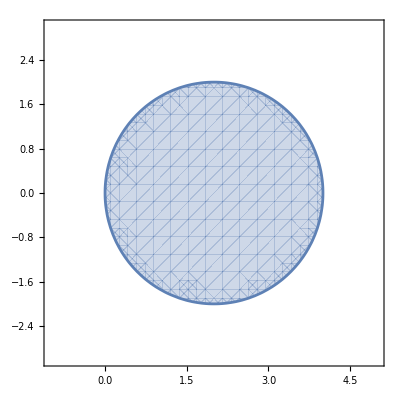

```mathematica
RegionPlot[(x-2)^2+y^2<=4,{x,-1,5},{y,-3,3}]
```

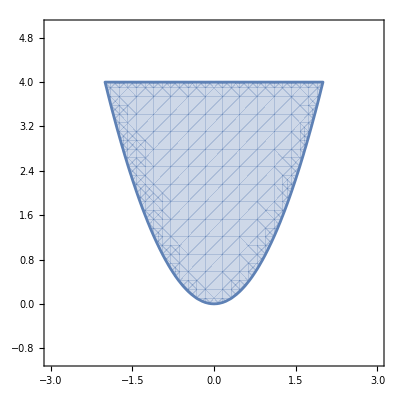

```mathematica
RegionPlot[(y>x^2)&&(y < 4),{x,-3,3},{y,-1,5}]
```

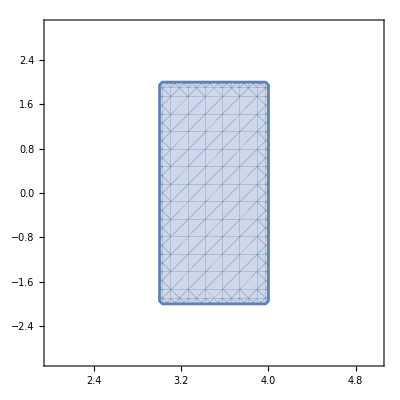

```mathematica
RegionPlot[(3<x<4)&&(-2<y<2),{x,2,5},{y,-3,3}]
```

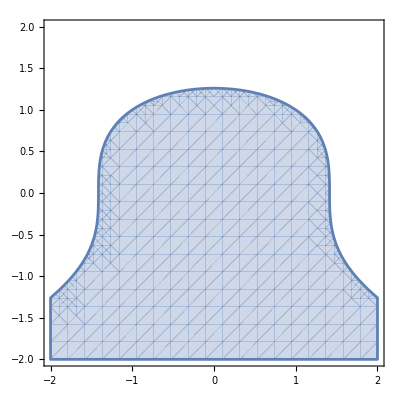

```mathematica
RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2}]
```

## Zadanie 4

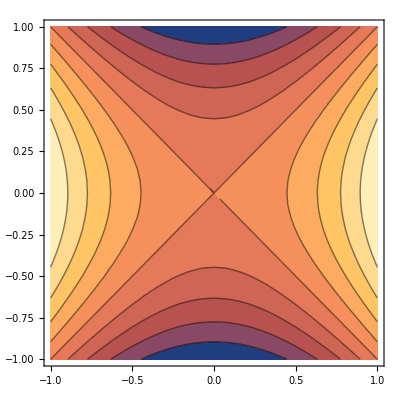

```mathematica
ContourPlot[x^2-y^2,{x,-1,1},{y,-1,1}]
```

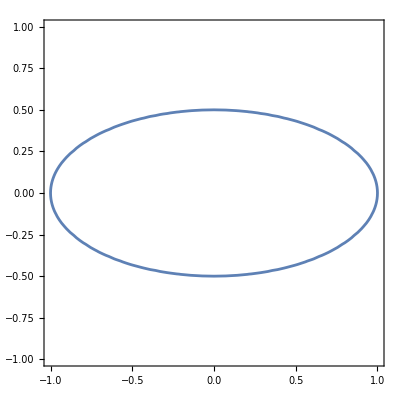

```mathematica
ContourPlot[x^2+(2 y)^2==1,{x,-1,1},{y,-1,1}]
```

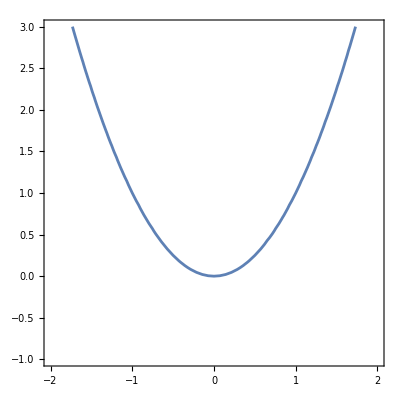

```mathematica
ContourPlot[x^2==y,{x,-2,2},{y,-1,3}]
```

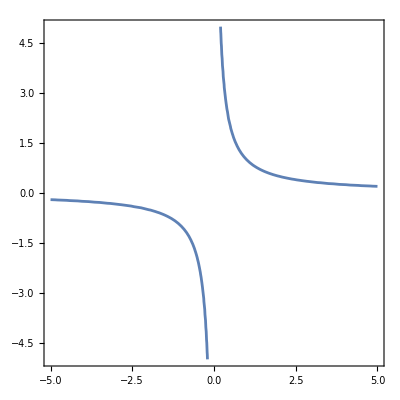

```mathematica
ContourPlot[x y==1,{x,-5,5},{y,-5,5}]
```

## Zadanie 5

```mathematica
RegionPlot3D[x^2+y^2+z^2<=1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[x^2+y^2<=z^2,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[x^2+y^2<= 1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

## Zadanie 6

```mathematica
torus[{R_,r_},{x_,y_,z_}]:=(x^2+y^2+z^2+R^2-r^2)^2==4 R^2(x^2+z^2);

ContourPlot3D[
Evaluate[torus[{6,3},{x,y,z}]],
{x,-10,10},{y,-10,10},{z,-10,10}
]
```

-Graphics3D-

```mathematica
ContourPlot3D[z==x^2-y^2,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
ContourPlot3D[z==x^2+y^2,{x,-1,1},{y,-1,1},{z,0,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2-z^2==1,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2-z^2==-1,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

## Zadanie 7

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/10},{t,0,10π}]
```

-Graphics3D-